```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
```

#### Solving for the pion γ and β in terms of kinetic energy of pion Eπ (arbitrary parameter but of order ~ 500 MeV)

```mathematica
Solve[(γ-1)mπ==Eπ/.γ->1/Sqrt[1-β^2],β]//Simplify
```

{{β→-(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)},{β→(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}}

#### Define Emax (in the simplest approximation)

```mathematica
Emax:=((2me*β^2 γ^2)/.{γ->1/Sqrt[1-β^2]})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

```mathematica
Emax//FullSimplify
```

(2 Eπ me (Eπ+2 mπ))/mπ^2

```mathematica
dσdE=2Pi*(α^2 Z^2)/(me*β^2*Ed^2)(1-β^2 Ed/emax)//FullSimplify;
```

```mathematica
dEdx=Integrate[dσdE*n*Ed,Ed]//FullSimplify
```

(2 n π Z^2 α^2 (-(Ed β^2)/emax+Log[Ed]))/(me β^2)

```mathematica
stoppingpower=2Pi*(n*Z^2*α^2)/(me*β^2)(Log[Emaxfull/emin]-β^2)/.{γ->1/Sqrt[1-β^2]}/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)//FullSimplify;
```

#### Express number density in units of MeV

```mathematica
Convert[10^23/Centimeter^3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

8.×10^-10 ElectronVolt^3 Mega^3

#### Plot of stopping power, with numerics

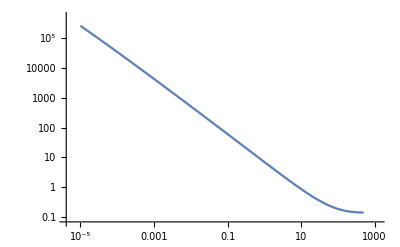

```mathematica
LogLogPlot[stoppingpower/.{n->8,me->0.511,M->0.511,emin->10^-10,α->1/137,mπ->140,Z->1},{Eπ,0.00001,500}]
```

#### Comparing with the PDG, which measures dE/dx in MeV g^-1 cm^2 for differing materials (normalized by density) and finds O(1) values:

```mathematica
Convert[0.15(Mega ElectronVolt)^2*( (5*10^9 Gram)/Centimeter^3)^-1*1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt*Centimeter^2/Gram)]
```

(1.5 Centimeter^2 ElectronVolt Mega)/Gram

#### Range for a typical value of Eπ

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,M->0.511,emin->10^-6,α->1/137,mπ->140,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{10^2,10^3,10^4,10^5}}]
```

{7.69793×10^-9 Centimeter,1.06507×10^-7 Centimeter,8.88791×10^-7 Centimeter,7.69788×10^-6 Centimeter}

#### Plot R for varying values of Eπ

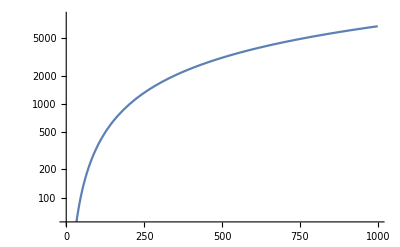

```mathematica
LogPlot[NIntegrate[stoppingpower^-1/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0,d}],{d,0,1000}]
```

#### In terms of PDG units, which gives range (normalized by density) of order O(1000 gm cm^-2):

```mathematica
Convert[3000/(Mega ElectronVolt)*( (5*10^9 Gram)/Centimeter^3)*(200 Mega ElectronVolt*Fermi),Gram/Centimeter^2]
```

(300 Gram)/Centimeter^2

#### Now incorporate Pauli-Blocking.

#### For relativistic fermi gas:

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
npaulirel
```

Ed^3/(3 π^2)-(Ed^2 Ef)/π^2+(Ed Ef^2)/π^2

```mathematica
npaulirel/.{Ed->Ef}
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8//N
```

6.18734

```mathematica
plotrel=Plot[npaulirel/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Using naive pauliblocking factor (Ed/Ef), where Ed is deposited energy

```mathematica
naiveplotrel=Plot[n*(Ed/Ef)/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Comparing “effective” number density available for depositing energy Ed, with upper end of plot being Fermi energy.

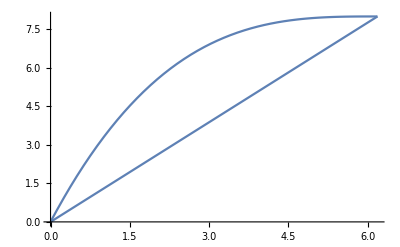

```mathematica
Show[plotrel,naiveplotrel]
```

```mathematica
dσdE
```

(2 π Z^2 α^2)/(Ed^2 me β^2)

#### We must be careful about the upper bound Emax...for electron scattering, this is the minimum of a quantum (uncertainty) and kinetic bounds. No matter what, though, Emax is less than the fermi energy, so I must be scattering into the Fermi sea.

```mathematica
Emaxfull
```

(2 M β^2 γ^2)/(1+M^2/mπ^2+(2 M γ)/mπ)

```mathematica
dσdE
```

(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 me β^2)

```mathematica
maximum:=Min[{2*me*γ^2*α^2,me}]
```

```mathematica
dedxpauli:=Integrate[dσdE*npaulirel*Ed,{Ed,(12 n π α^3)/(Ef me*β^2),emax}]/.{emax->maximum,Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

#### Plots of R_ϵ due to Coulomb for different particles.

```mathematica
muoncoulomb=Table[{x/1000,Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->100,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]/Centimeter},{x,fSpace[500,10^9,100]}];
```

```mathematica
muoncoulombplot=Interpolation[muoncoulomb];
```

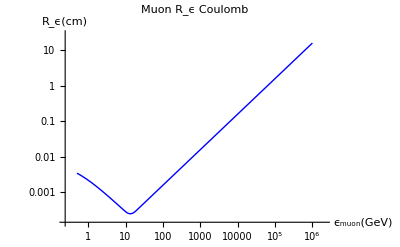

```mathematica
LogLogPlot[muoncoulombplot[x],{x,0.5,10^6},PlotStyle->{Thick,Blue},AxesLabel->{"ϵ_muon(GeV)","R_ϵ(cm)"},PlotLabel->"Muon R_ϵ Coulomb"]
```

#### Electrons

```mathematica
electroncoulomb=Table[{x/1000,Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->0.511,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]/Centimeter},{x,fSpace[10,10^9,100]}];
```

```mathematica
electroncoulombplot=Interpolation[electroncoulomb];
```

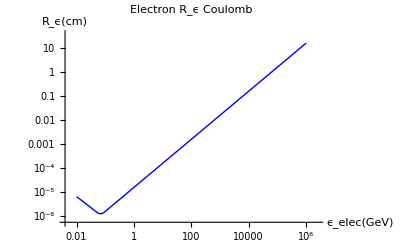

```mathematica
LogLogPlot[electroncoulombplot[x],{x,0.01,10^6},PlotStyle->{Thick,Blue},AxesLabel->{"ϵ_elec(GeV)","R_ϵ(cm)"},PlotLabel->"Electron R_ϵ Coulomb"]
```

#### Compare with nondegenerate stopping power.

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,M->0.511,emin->10^-6,α->1/137,mπ->140,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{10^2,10^3,10^4,10^5}}]
```

{8.02412×10^-9 Centimeter,1.12805×10^-7 Centimeter,9.32226×10^-7 Centimeter,8.02153×10^-6 Centimeter}

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,M->0.511,emin->10^-6,α->1/137,mπ->0.5,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{10^2,10^3,10^4,10^5}}]
```

{1.11501×10^-8 Centimeter,9.82807×10^-8 Centimeter,8.78594×10^-7 Centimeter,7.94365×10^-6 Centimeter}